```mathematica
filenames={"Table_TwoHerbicides_high_Stochastic_control6_sexualReproduction1_seedbank1_cost1_300_cost2_300_kCost1_5_kCost2_5_kHerb1_5_kHerb2_5_fieldsize10000.txt",
"Table_TwoHerbicides_high_Stochastic_control8_sexualReproduction1_seedbank1_cost1_300_cost2_300_kCost1_5_kCost2_5_kHerb1_5_kHerb2_5_fieldsize10000.txt"};
```

```mathematica
data=Table[Import[NotebookDirectory[]<>"../data/"<>filenames⟦i⟧,"CSV"],{i,1,Length[filenames],1}];
```

## Plant density/m^2

```mathematica
plottab=Table[gatherruns=GatherBy[data⟦j,2;;,{1,6,2}⟧,Last];
Show[ListLogPlot[Table[gatherruns⟦i⟧⟦All,2⟧,{i,1,1000,1}],Joined->True,PlotStyle->Directive[Opacity[0.05],RGBColor["#687988"]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.003],16],FrameLabel->None],
ListLogPlot[gatherruns⟦1001⟧⟦All,2⟧,Joined->True,Mesh->True,PlotStyle->Directive[Full,RGBColor["#3C4C59"]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.003],16],FrameLabel->None],PlotRange->{{0,30},{-6,6}},Axes->None],{j,1,Length[data],1}];
```

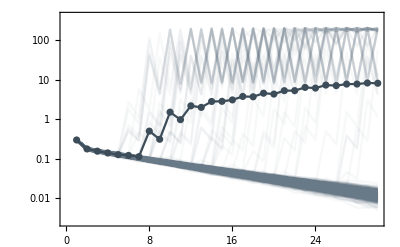
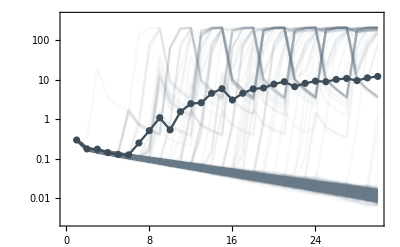

```mathematica
{{plottab⟦1⟧,plottab⟦2⟧}}
```

```mathematica
plottab⟦2⟧
```

-Graphics-